### Parte 1 (Baterias de 1 a 5)

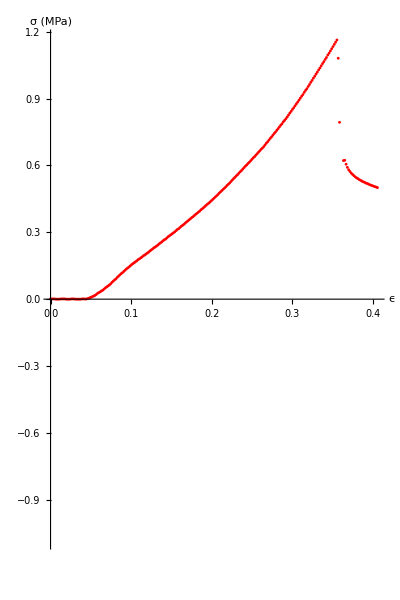

```mathematica
bat1=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt1\\BAT1.xls"];
d1=13.16;
h1=30.83;
fTAV1=Table[{bat1[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d1^2 (* A[mm^2]*),0.5 (* v[mm/s] *)},{i,1,Length[bat1]}];
deltaSt1=Table[{fTAV1[[i]][[2]]fTAV1[[i]][[4]],fTAV1[[i]][[1]]/fTAV1[[i]][[3]]},{i,1,Length[bat1]}];
deformTensao=Table[{deltaSt1[[i]][[1]]/h1,deltaSt1[[i]][[2]]},{i,1,Length[bat1]}];
g1=ListPlot[deformTensao,AxesLabel->{"ϵ","σ (MPa)"},PlotStyle->{Red,PointSize[.005]},AspectRatio->1.5]
```

```mathematica
bat2=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt1\\BAT2.xls"];
d2=12.89;
h2=31.34;
fTAV1=Table[{bat1[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d2^2 (* A[mm^2]*),0.5 (* v[mm/s] *)},{i,1,Length[bat1]}];
deltaSt1=Table[{fTAV1[[i]][[2]]fTAV1[[i]][[4]],fTAV1[[i]][[1]]/fTAV1[[i]][[3]]},{i,1,Length[bat1]}];
deformTensao=Table[{deltaSt1[[i]][[1]]/h2,deltaSt1[[i]][[2]]},{i,1,Length[bat1]}];
g2=ListPlot[deformTensao,PlotStyle->{Purple,PointSize[.005]}];
```

```mathematica
bat3=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt1\\BAT3.xls"];
d3=13.2;
h3=30.84;
fTAV1=Table[{bat1[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d3^2 (* A[mm^2]*),0.5 (* v[mm/s] *)},{i,1,Length[bat1]}];
deltaSt1=Table[{fTAV1[[i]][[2]]fTAV1[[i]][[4]],fTAV1[[i]][[1]]/fTAV1[[i]][[3]]},{i,1,Length[bat1]}];
deformTensao=Table[{deltaSt1[[i]][[1]]/h3,deltaSt1[[i]][[2]]},{i,1,Length[bat1]}];
g3=ListPlot[deformTensao,PlotStyle->{Blue,PointSize[.005]}];
```

```mathematica
bat4=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt1\\BAT4.xls"];
d4=13.25;
h4=31.8;
fTAV1=Table[{bat1[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d4^2 (* A[mm^2]*),0.5 (* v[mm/s] *)},{i,1,Length[bat1]}];
deltaSt1=Table[{fTAV1[[i]][[2]]fTAV1[[i]][[4]],fTAV1[[i]][[1]]/fTAV1[[i]][[3]]},{i,1,Length[bat1]}];
deformTensao=Table[{deltaSt1[[i]][[1]]/h4,deltaSt1[[i]][[2]]},{i,1,Length[bat1]}];
g4=ListPlot[deformTensao,PlotStyle->{Orange,PointSize[.005]}];
```

```mathematica
bat5=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt1\\BAT5.xls"];
d5=13.2;
h5=30.84;
fTAV1=Table[{bat1[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d5^2 (* A[mm^2]*),0.5 (* v[mm/s] *)},{i,1,Length[bat1]}];
deltaSt1=Table[{fTAV1[[i]][[2]]fTAV1[[i]][[4]],fTAV1[[i]][[1]]/fTAV1[[i]][[3]]},{i,1,Length[bat1]}];
deformTensao=Table[{deltaSt1[[i]][[1]]/h5,deltaSt1[[i]][[2]]},{i,1,Length[bat1]}];
g5=ListPlot[deformTensao,PlotStyle->{Magenta,PointSize[.005]}];
```

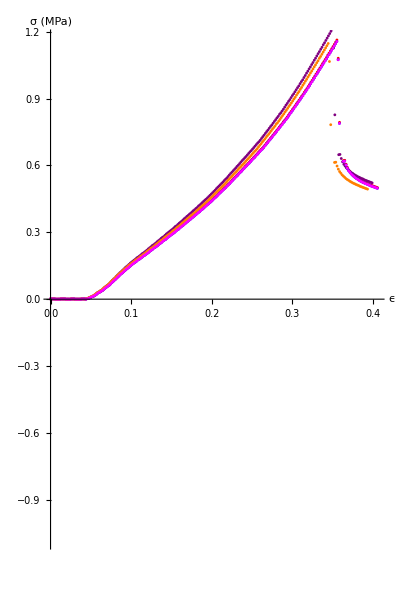

```mathematica
Show[g1,g2,g3,g4,g5,AspectRatio->1.5]
```

### Parte 2 (Baterias de 6 a 10)

```mathematica
bat6=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt2\\BAT6.xls"];
```

```mathematica
bat7=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt2\\BAT7.xls"];
```

```mathematica
bat8=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt2\\BAT8.xls"];
```

```mathematica
bat9=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt2\\BAT9.xls"];
```

```mathematica
bat10=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt2\\BAT10.xls"];
```

### Parte 3 (Baterias de 11 a 15)

```mathematica
bat11=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt3\\BAT11.xls"];
```

```mathematica
bat12=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt3\\BAT12.xls"];
```

```mathematica
bat13=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt3\\BAT13.xls"];
```

```mathematica
bat14=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt3\\BAT14.xls"];
```

```mathematica
bat15=Import["C:\\Users\\renan\\Desktop\\576\\bateries\\xls\\pt3\\BAT15.xls"];
```